```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Parameters*)
kmax = 30; (*SF*)
k0=2; (*SF*)
alpha=3.5; (*SF*)
alphamin=2.01; (*SF*)
alphamax=6.5; (*SF*)

nmax = 15; (*ER*)
meandeg=10; (*ER*)
meandegmin=0.1; (*ER*)
meandegmax=5; (*ER*)
threshmin=3; (*Attacks*)
threshmax=10; (*Attacks*)
```

```mathematica
(*Functions Attacks*) 
(* I do not use HeavisideTheta[x] because HeavisideTheta[0] is not defined *)
PhiHubs[k_,thresh_]:=Which[k<=thresh,1,k>thresh,0]
PhiLowDeg[k_,thresh_]:=Which[k<=thresh,0,k>thresh,1]
```

```mathematica
(*Functions SF*)
meandegreeSF[alpha_,k0_,kmax_]:=(HurwitzZeta[alpha-1,k0]-HurwitzZeta[alpha-1,kmax+1])/(HurwitzZeta[alpha,k0]-HurwitzZeta[alpha,kmax+1])
pkSF[alpha_,k0_,kmax_]:=Table[1/(HurwitzZeta[alpha,k0]-HurwitzZeta[alpha,kmax+1])i^-alpha,{i,k0,kmax}]
lhsSF:=Range[0.01,1,0.02]; 
rhsSF[alpha_,k0_,kmax_,thresh_]:=Table[∑_(n=k0)^(kmax-1) (1 - PhiHubs[n+1,thresh]+PhiHubs[n+1,thresh]*1/(meandegreeSF[alpha,k0,kmax]-k0*pkSF[alpha,k0,kmax][[1]])(n+1)pkSF[alpha,k0,kmax][[n+1+1-k0]]*u^n),{u,0.01,1,0.02}];
GCSF[alpha_,k0_,kmax_,thresh_,u_]:=∑_(n=k0)^kmax (PhiHubs[n,thresh]*pkSF[alpha,k0,kmax][[n+1-k0]]*(1-u^n))
GiantComponentVsThreshSF[alpha_,k0_,kmax_,threshmin_,threshmax_]:=Table[GCSF[alpha,k0,kmax,varthresh,u]/.NSolve[u-1/(meandegreeSF[alpha,k0,kmax]-k0*pkSF[alpha,k0,kmax][[1]])∑_(n=k0)^(kmax-1) (n+1)pkSF[alpha,k0,kmax][[n+1+1-k0]](1 - PhiHubs[n+1,varthresh]+PhiHubs[n+1,varthresh]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varthresh,threshmin,threshmax,1}]
GiantComponentVsAlpha[thresh_,k0_,kmax_,alphamin_,alphamax_]:=Table[GCSF[varalpha,k0,kmax,thresh,u]/.NSolve[u-1/(meandegreeSF[varalpha,k0,kmax]-k0*pkSF[varalpha,k0,kmax][[1]])∑_(n=k0)^(kmax-1) (n+1)pkSF[varalpha,k0,kmax][[n+1+1-k0]](1 -  PhiHubs[n+1,thresh]+ PhiHubs[n+1,thresh]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varalpha,alphamin,alphamax,0.1}]
```

```mathematica
(*Functions ER*)
pkER[meandeg_,nmax_]:=Table[(meandeg^i*Exp[-meandeg])/(i!)1/(∑_(k=0)^nmax (meandeg^k*Exp[-meandeg])/(k!)),{i,0,nmax}]
lhsER:=Range[0.01,1,0.02];
rhsER[meandeg_,nmax_,thresh_]:=Table[∑_(n=0)^(nmax-1) 1/meandeg(n+1)pkER[meandeg,nmax][[n+1+1]]*(1 - PhiHubs[n+1,thresh]+PhiHubs[n+1,thresh]*u^n),{u,0.01,1,0.02}];
GCER[meandeg_,nmax_,thresh_,u_]:=∑_(n=0)^nmax (PhiHubs[n,thresh]*pkER[meandeg,nmax][[n+1]]*(1-u^n))
GiantComponentVsThreshER[meandeg_,nmax_,threshmin_,threshmax_]:=Table[GCER[meandeg,nmax,varthresh,u]/.NSolve[u-∑_(n=0)^(nmax-1) 1/meandeg(n+1)pkER[meandeg,nmax][[n+1+1]](1 - PhiHubs[n+1,varthresh]+PhiHubs[n+1,varthresh]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varthresh,threshmin,threshmax,1}]
GiantComponentVsMeanDegreeER[thresh_,nmax_,meandegmin_,meandegmax_]:=Table[GCER[varmeandeg,nmax,thresh,u]/.NSolve[u-∑_(n=0)^(nmax-1) 1/varmeandeg(n+1)pkER[varmeandeg,nmax][[n+1+1]](1 - PhiHubs[n+1,thresh]+PhiHubs[n+1,thresh]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varmeandeg,meandegmin,meandegmax,0.1}]
```

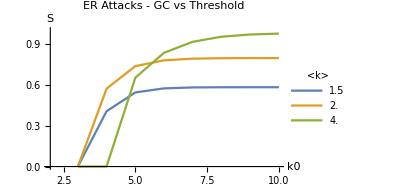

```mathematica
(*Attacks on ER nets*)
meandeg1=1.5;
meandeg2=2.;
meandeg3=4.;
ListPlot[ 
{GiantComponentVsThreshER[meandeg1,nmax,threshmin,threshmax],
GiantComponentVsThreshER[meandeg2,nmax,threshmin,threshmax],
GiantComponentVsThreshER[meandeg3,nmax,threshmin,threshmax]},
PlotRange->{{-1+threshmin,threshmax},{0,1}},DataRange->{threshmin,threshmax},
AxesLabel->{"k0","S"},PlotLabel->"ER Attacks - GC vs Threshold",
ImageSize->300,Joined->True,
PlotLegends->Placed[PointLegend[Automatic,{meandeg1,meandeg2,meandeg3},LegendLabel->"<k>"],Automatic]]
```

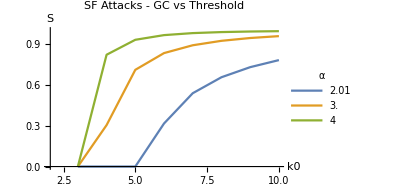

```mathematica
(*Attacks on SF nets*)
alpha1=2.01;
alpha2=3.;
alpha3=4;
ListPlot[ 
{GiantComponentVsThreshSF[alpha1,k0,kmax,threshmin,threshmax],
GiantComponentVsThreshSF[alpha2,k0,kmax,threshmin,threshmax],
GiantComponentVsThreshSF[alpha3,k0,kmax,threshmin,threshmax]},
PlotRange->{{-1+threshmin,threshmax},{0,1}},DataRange->{threshmin,threshmax}, 
AxesLabel->{"k0","S"}, PlotLabel->"SF Attacks - GC vs Threshold",
ImageSize->300,Joined->True,
PlotLegends->Placed[PointLegend[Automatic,{alpha1,alpha2,alpha3},LegendLabel->"α"],Automatic]]
```

```mathematica
(*Comparisson of random removal vs attacks ER*)
```